# Hyperpolarized Activated

## Parameters

```mathematica
hParameters={gh->0.037,eh->-10,cr->0.33,vr->-70,vkr->-110,sr->7,skr->-13,cm->1700(*unit conversion*)};
```

## Steady State Equations

```mathematica
(*Voltage Dependence*)
rinfinite[V_]:=1/(1+Exp[(V-vr)/sr])/.hParameters;
(*relaxation*)
kr[V_]:=cr*(1+Exp[(V-vkr)/skr])/.hParameters;
```

## Initial Activations and Inactivations

```mathematica
(*solve for initial activation by holding at holding voltage until system reaches steady state*)initialActivation=NDSolve[{r'[t]==(rinfinite[-40]-r[t])*kr[-40],r[0]==0}/.hParameters,r[t],{t,0,100000}];
```

```mathematica
(*getting a value for the inital activation at the holding voltage -40mV*)initialAct=r[t]/.initialActivation[[1,All]]/.t->100000
```

0.0135769

```mathematica
(*step to -110,-100, etc. mV and repeat the process*){stepActivation120,stepActivation110,stepActivation100,stepActivation90,stepActivation80,stepActivation70}=Table[NDSolve[{r'[t]==(rinfinite[stepVoltage]-r[t])*kr[stepVoltage],r[0]==0.013576916943744367}/.hParameters,r[t],{t,0,100000}],{stepVoltage,{-120,-110,-100,-90,-80,-70}}];
```

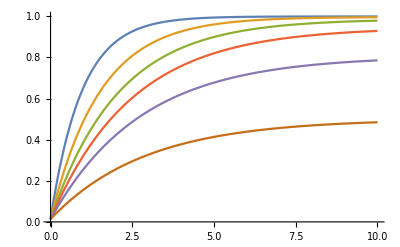

```mathematica
(*this is a plot of activation values going from their values at -40mV to their values at their step voltages. We can see that more negative steps lead to higher and quicker activations*)Plot[{Evaluate[r[t]/.stepActivation120[[1,All]]],Evaluate[r[t]/.stepActivation110[[1,All]]],Evaluate[r[t]/.stepActivation100[[1,All]]],Evaluate[r[t]/.stepActivation90[[1,All]]],Evaluate[r[t]/.stepActivation80[[1,All]]],Evaluate[r[t]/.stepActivation70[[1,All]]]},{t,0,10}]
```

```mathematica
(*Differential Equations. These were done by setting initial activations and inactivations to the values we obtained by holding at -40mV above.*)
{memneg120,memneg110,memneg100,memneg90,memneg80,memneg70}=Table[NDSolve[{cm*V'[t]==(-(gh*(r[t])*(V[t]-eh))),r'[t]==(rinfinite[V[t]]-r[t])*kr[V[t]],r[0]==0.013576916943744367,V[0]==initV}/.hParameters,{V[t],r[t]},{t,0,20}],{initV,{-120,-110,-100,-90,-80,-70}}];
```

```mathematica
(*trying to hold at -40mV, and vary our initial activation. These calculations did not give us a graph matching the paper, and we decided in class that the NDSolve above was in line with what the paper attemtped to do.*)
{memFromAct120,memFromAct110,memFromAct100,memFromAct90,memFromAct80,memFromAct70}=Table[NDSolve[{cm*V'[t]==(-(gh*(r[t])*(V[t]-eh))),r'[t]==(rinfinite[-40]-r[t])*kr[-40],r[0]==stepAct,V[0]==-40}/.hParameters,{V[t],r[t]},{t,0,20}],{stepAct,{finalAct120[[1]],finalAct110[[1]],finalAct100[[1]],finalAct90[[1]],finalAct80[[1]],finalAct70[[1]]}}];
```

## Plots and Calculations

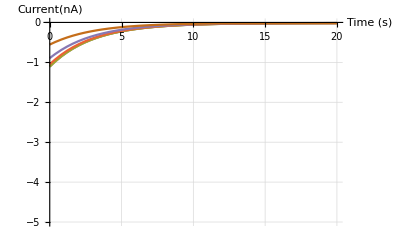

```mathematica
(*These plots correspond with the failed interpretation of the paper. Look at the below plot for the proper protocol's result.*)Plot[{Evaluate[0.037*r[t]*(V[t]+10)/.memFromAct120[[1,All]]/.hParameters],Evaluate[0.037*r[t]*(V[t]+10)/.memFromAct110[[1,All]]/.hParameters],Evaluate[0.037*r[t]*(V[t]+10)/.memFromAct100[[1,All]]/.hParameters],Evaluate[0.037*r[t]*(V[t]+10)/.memFromAct90[[1,All]]/.hParameters],Evaluate[0.037*r[t]*(V[t]+10)/.memFromAct80[[1,All]]/.hParameters],Evaluate[0.037*r[t]*(V[t]+10)/.memFromAct70[[1,All]]/.hParameters]},{t,0,20},PlotRange->{{0,20},{-5,0}},GridLines->Automatic,AxesLabel->{"Time (s)","Current(nA)"}]
```

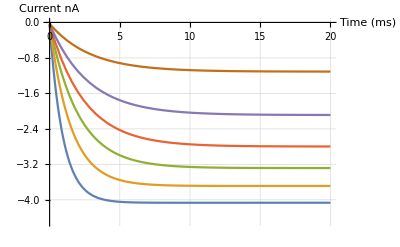

```mathematica
(*plot the current, ih. I'll put in gh and eh values directly.*)Plot[{Evaluate[.037*r[t]*(V[t]+10)/.memneg120[[1,All]]/.hParameters],Evaluate[.037*r[t]*(V[t]+10)/.memneg110[[1,All]]/.hParameters],Evaluate[.037*r[t]*(V[t]+10)/.memneg100[[1,All]]/.hParameters],Evaluate[.037*r[t]*(V[t]+10)/.memneg90[[1,All]]/.hParameters],Evaluate[.037*r[t]*(V[t]+10)/.memneg80[[1,All]]/.hParameters],Evaluate[.037*r[t]*(V[t]+10)/.memneg70[[1,All]]/.hParameters]},{t,0,20},PlotRange->{{0,20},{-4.5,0}},GridLines->Automatic,AxesLabel->{"Time (ms)","Current nA"}]
```

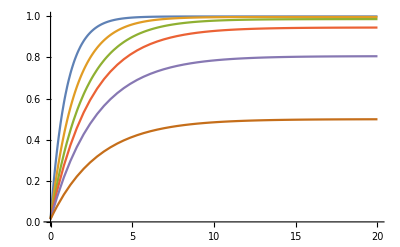

```mathematica
(*I want to see what all of those activation curves look like*)activationCurves=Plot[{Evaluate[r[t]/.memneg120/.hParameters],Evaluate[r[t]/.memneg110/.hParameters],Evaluate[r[t]/.memneg100/.hParameters],Evaluate[r[t]/.memneg90/.hParameters],Evaluate[r[t]/.memneg80/.hParameters],Evaluate[r[t]/.memneg70/.hParameters]},{t,0,20}]
```

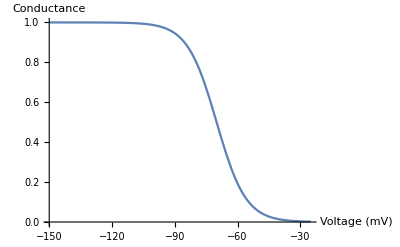

```mathematica
(*plot voltage dependence*)voltageDependence=Plot[1/(1+Exp[(V+70)/7]),{V,-150,-25},AxesLabel->{"Voltage (mV)","Conductance"},PlotRange->{{-150,-25},{0,1}}]
```

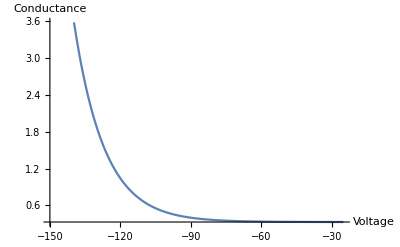

```mathematica
(*Plot relaxation. Needs to be normalized.*)relaxation=Plot[cr*(1+Exp[(V-vkr)/skr])/.hParameters,{V,-150,-25},AxesLabel->{"Voltage","Conductance"}]
```

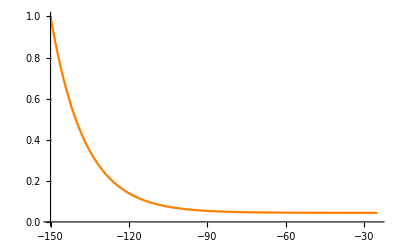

```mathematica
normRelaxation=Plot[Evaluate[kr[V]]/kr[-150]/.hParameters,{V,-150,-25},PlotRange->{{-150,-25},{0,1}},PlotStyle->Orange]
```

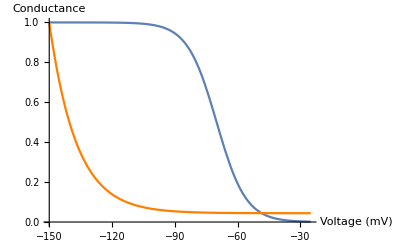

```mathematica
Show[voltageDependence,normRelaxation](*gotta normalize relaxation so they show up in the way portrayed in the paper*)
```